## Resistor Noise Preliminary Lab Report

Zachariah Sachs
CHEM 26701
16 April 2013

```mathematica
SetDirectory["/Users/Zachariah/Documents/CHEM 26701/ResNoiseLab"]
```

/Users/Zachariah/Documents/CHEM 26701/ResNoiseLab

```mathematica
vrvr=Import["V_R_vs_resist.csv"]
VOvF=Import["V_O_vs_freq.csv"]
```

{{50,0.0179115},{7500,0.0251448},{10000,0.0269902},{20000,0.0316499},{30000,0.0346797},{40000,0.0368715},{50000,0.0382411}}

{{0.,0.00189},{25000.,2.91},{50000.,2.02},{75000.,1.44},{100000.,1.03},{125000.,0.794},{150000.,0.64},{175000.,0.53},{200000.,0.431},{225000.,0.355},{250000.,0.295},{275000.,0.252},{300000.,0.214}}

```mathematica
VRvR=Delete[vrvr,1]
```

{{7500,0.0251448},{10000,0.0269902},{20000,0.0316499},{30000,0.0346797},{40000,0.0368715},{50000,0.0382411}}

```mathematica
VRvR
```

{{7500,0.0251448},{10000,0.0269902},{20000,0.0316499},{30000,0.0346797},{40000,0.0368715},{50000,0.0382411}}

1) We are asked particularly to provide a noise signal and power spectrum. I vaguely remember hearing something about saving a screen-shot. If we were supposed to take a screen shot of the ResistorNoise program as we were taking measurements, we didn’t. Should we get the noise signal and power spectrum from another group?

2) and 3) a) Here is a plot of the gain characteristics of the amplifier as “Output vs. Frequency” and a plot of RMS noise as “Resistor Noise vs. Resistance”.

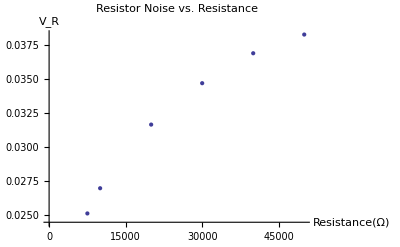

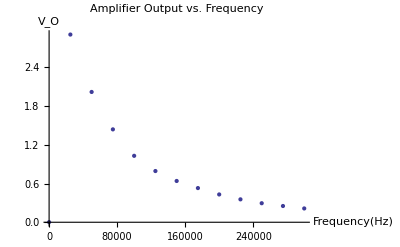

```mathematica
ListPlot[VRvR,PlotLabel->"Resistor Noise vs. Resistance",AxesLabel->{"Resistance(Ω)","V_R"}]
ListPlot[VOvF,PlotLabel->"Amplifier Output vs. Frequency",AxesLabel->{"Frequency(Hz)","V_O"}]
```

```mathematica
VO:=Interpolation[VOvF,InterpolationOrder->0];(**functionalize V_O v F **)
Vi:=5.5899795*10^(-2); (** function generator voltage **)
cap:=60*10^(-12); (** capacitance of coax in F **)
g[freq_,res_]:=(VO[freq]/Vi)^2/(1+(2*Pi*freq*res*cap)^2); (** integrand from Equation (13) **)
df[res_]:=(25000/2)Sum[g[n*25000,res]+g[(n+1)*25000,res],{n,0,11}]; (** Trapezoid rule **)
dF[res_]:=(25000/6)Sum[g[n*25000,res]+4g[(n+(1/2))*25000,res]+g[(n+1)*25000,res],{n,0,11}]; (** Simpson's Rule **)
VG:=vrvr[[1]][[2]]; (** amplifier noise **)
VR:=Interpolation[VRvR,InterpolationOrder->0]; (** functionalize V_R v R **)
a:=0.01;
T:=295;
```

```mathematica
Gr[res_]:=((a*VR[res])^2-(a*VG)^2)/df[res]; (** aiming towards a fit **)
gR[res_]:=((a*VR[res])^2-(a*VG)^2)/dF[res]; (** aiming towards a fit **)
```

```mathematica
fIt=List[{7500,Gr[7500]},{10000,Gr[10000]},{20000,Gr[20000]},{30000,Gr[30000]},{40000,Gr[40000]},{50000,Gr[50000]}];
fiT=List[{7500,gR[7500]},{10000,gR[10000]},{20000,gR[20000]},{30000,gR[30000]},{40000,gR[40000]},{50000,gR[50000]}];
```

```mathematica
V2[res_]:=(a*VR[res])^2-(a*VG)^2; (** Equation 14 **)
MSV=List[{7500,V2[7500]},{10000,V2[10000]},{20000,V2[20000]},{30000,V2[30000]},{40000,V2[40000]},{50000,V2[50000]}];
```

3)b) Here is a plot of MSV. I don’t know how this is useful. We can’t fit this data by itself. We need to use Equations (9) and (14) to get a relation linear in resistance.

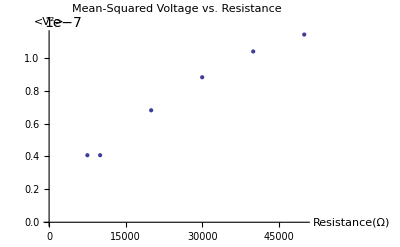

```mathematica
ListPlot[MSV,PlotLabel->"Mean-Squared Voltage vs. Resistance",AxesLabel->{"Resistance(Ω)","<V^2>"}]
```

```mathematica
modEl=LinearModelFit[fIt,x,x]
modeL=LinearModelFit[fiT,x,x]
```

FittedModel[8.69176×10^-17+1.81857×10^-20 x]

FittedModel[1.07151×10^-16+2.02486×10^-20 x]

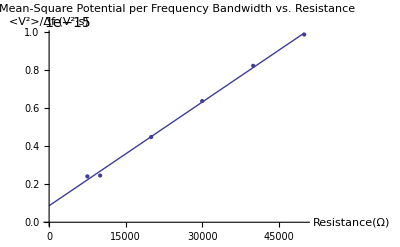

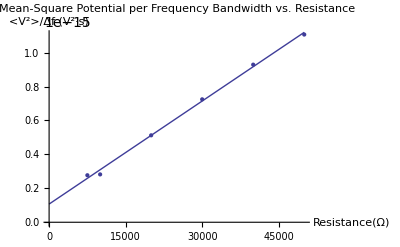

```mathematica
Show[ListPlot[fIt,PlotLabel->"Mean-Square Potential per Frequency Bandwidth vs. Resistance",AxesLabel->{"Resistance(Ω)","<V^2>/Δf (V^2·s)"}],Plot[modEl["BestFit"],{x,0,50000},PlotLabel->"Mean-Square Potential per Frequency Bandwidth vs. Resistance",AxesLabel->{"Resistance(Ω)","<V^2>/Δf (V^2·s)"}]]
Show[ListPlot[fiT,PlotLabel->"Mean-Square Potential per Frequency Bandwidth vs. Resistance",AxesLabel->{"Resistance(Ω)","<V^2>/Δf (V^2·s)"}],Plot[modeL["BestFit"],{x,0,50000},PlotLabel->"Mean-Square Potential per Frequency Bandwidth vs. Resistance",AxesLabel->{"Resistance(Ω)","<V^2>/Δf (V^2·s)"}]]
(** V^2*s/Ω=W*s=J so the slope is in Joules **)
```

4) Following my suggestion above, below is the value of Boltzmann’s constant obtained by fitting our data to the theory. I could probably go through the standard error in some of the simple calculations, but I do not know how to propogate it through integrals or linear fits. Are there functions in Mathematica or MATLAB that could help with this?

```mathematica
1.8185692610437984*^-20/(4*T) (** Boltzmann's constant using the Trapezoid rule **)
2.0248611968274995*^-20/(4*T) (** Boltzmann's constant using Simpson's rule **)
```

1.54116×10^-23

1.71598×10^-23

```mathematica
kB:=1.3806488*10^(-23); (** Boltzmann's Constant in J/K **)
```

```mathematica
((1.5411603907150834*^-23)-kB)/kB*100
```

11.6783

5) The average value from the calculations above for Boltzmann’s constant is above the accepted value. In terms of data, this might be due to the number of frequencies at which we measured the noise. We could have gotten a more precise gain characteristic and value of df if we had taken more measurements. 
During initial measurements of resistor noise, we were getting an unwanted periodic signal, perhaps from some electrical signal in the lab which we were not able to pin down. This extra “noise” would tend to give a higher value of RMS voltage than expected. Perhaps this same noise was occuring when we took the gain characteristic of the amplifier, and so we got high measurements for V_O. This would give an inflated value of Δf, and I think that based on the shape of the gain characteristic, would give a larger slope than expected in the fit of mean-square voltage over Δf vs. resistancefrom which we calculated Boltzmann’s constant.

6) Do we want to minimize the deviation of the calculated value of Boltzmann’s constant by eliminating error from our measurements, or do we want to generally minimize the uncertainty caused by resistor noise in any measurement involving electronics? If the former, as I said, we could take more measurements to smooth out the statistics. If the latter, we can’t. We can try to minimize the resistance in various ways, but for a fixed resistance, there is always a minimum abount of noise fundamental to circuits.

7) The Fourier transform essentially takes any time-dependent signal, looks at its “Fourier series”, an infinite series of periodic functions, and spits out for any particular frequency the magnitude of that frequency’s contribution to the Fourier series. That is, the fourier transform gives the “frequency spectrum” of the signal. The shape of noise (intensity) signals is messy; the Fourier transform, the power spectrum, has a shape more condusive to evaluation.

8) The ensemble in this case is an electrical circuit. The microscopic elements, electrons, can occuy microstates bound to various nuclei in conducting material. We get to measure macroscopic properties of this ensemble, like current or potential.

9) This lab give another stat-mech way of finding Boltzmann’s constant, which is obviously fundamental to stat-mech and thermodynamics, and thus chemistry. Noise in circuit elements probably has logical parallels in measurements of gases; for example, deviation from ideal-gas behavior could be thought of as “noise” due to particle size or inter-particle forces.